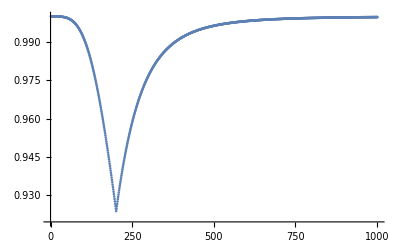

```mathematica
L=4;
g=2;
ks=Table[(2*n*Pi)/L,{n,-L/2,(L/2-1)}];an = Table[-Total[Table[k=ks[[l]];Sqrt[g^2+(J)^2+(2*J*g*Cos[k])],{l,1,Length[ks]}]],{J,0,10,.01}];

op[n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2,2}:=KroneckerProduct[IdentityMatrix[2^(k-1),SparseArray],a,IdentityMatrix[2^(n-k),SparseArray]];
sz[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[3]];
sx[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[1]];
HH[n_Integer/;n≥3,g_,J_]:=-g*Sum[sz[n,k],{k,n}]-J*Sum[sx[n,k].sx[n,Mod[k+1,n,1]],{k,n}];
num =Table[kk=HH[4,g,J]//Eigenvalues//Min;kk,{J,0,10,.01}];
p4=ListPlot[an/num, PlotRange->All]
```

```mathematica
L=4;
{g,J}={1,11};
ks=Table[(2*n*Pi)/L,{n,-L/2,(L/2-1)}];
Eg=Total[Table[k=ks[[l]];If[g==J && k==-L/2,0,-Sqrt[g^2+(J)^2+(2*J*g*Cos[k])]],{l,1,Length[ks]}]]//N
```

-44.0907

```mathematica
Min[HH[4,g,J]//Eigenvalues]//N
```

-44.0912

```mathematica
L=4;
g=2;
ks=Table[(2*n*Pi)/L,{n,-L/2,(L/2-1)}];an = Table[-Total[Table[k=ks[[l]];If[g==J && k==-L/2,0,Sqrt[g^2+(J)^2+(2*J*g*Cos[k])]],{l,1,Length[ks]}]],{J,0,10,.01}];

op[n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2,2}:=KroneckerProduct[IdentityMatrix[2^(k-1),SparseArray],a,IdentityMatrix[2^(n-k),SparseArray]];
sz[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[3]];
sx[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[1]];
HH[n_Integer/;n≥3,g_,J_]:=-g*Sum[sz[n,k],{k,n}]-J*Sum[sx[n,k].sx[n,Mod[k+1,n,1]],{k,n}];
num =Table[kk=HH[4,g,J]//Eigenvalues//Min;kk,{J,0,10,.01}];
ListPlot[an/num, PlotRange->All]
```

-Graphics-

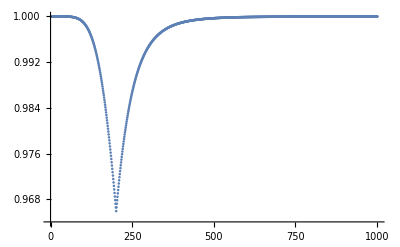

```mathematica
L=6;
g=2;
ks=Table[(2*n*Pi)/L,{n,-L/2,(L/2-1)}];an = Table[-Total[Table[k=ks[[l]];If[g==J && k==-L/2,0,Sqrt[g^2+(J)^2+(2*J*g*Cos[k])]],{l,1,Length[ks]}]],{J,0,10,.01}];

op[n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2,2}:=KroneckerProduct[IdentityMatrix[2^(k-1),SparseArray],a,IdentityMatrix[2^(n-k),SparseArray]];
sz[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[3]];
sx[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[1]];
HH[n_Integer/;n≥3,g_,J_]:=-g*Sum[sz[n,k],{k,n}]-J*Sum[sx[n,k].sx[n,Mod[k+1,n,1]],{k,n}];
num =Table[kk=HH[L,g,J]//Eigenvalues//Min;kk,{J,0,10,.01}];
p6=ListPlot[an/num, PlotRange->All]
```

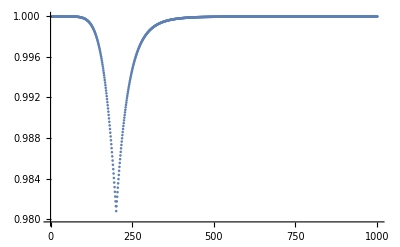

```mathematica
L=8;
g=2;
ks=Table[(2*n*Pi)/L,{n,-L/2,(L/2-1)}];an = Table[-Total[Table[k=ks[[l]];If[g==J && k==-L/2,0,Sqrt[g^2+(J)^2+(2*J*g*Cos[k])]],{l,1,Length[ks]}]],{J,0,10,.01}];

op[n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2,2}:=KroneckerProduct[IdentityMatrix[2^(k-1),SparseArray],a,IdentityMatrix[2^(n-k),SparseArray]];
sz[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[3]];
sx[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[1]];
HH[n_Integer/;n≥3,g_,J_]:=-g*Sum[sz[n,k],{k,n}]-J*Sum[sx[n,k].sx[n,Mod[k+1,n,1]],{k,n}];
num =Table[kk=HH[L,g,J]//Eigenvalues//Min;kk,{J,0,10,.01}];
p8=ListPlot[an/num, PlotRange->All]
```

```mathematica
Show[{p4,p6,p8}]
```

```mathematica
*This effect is due to the omission of the correlator term... see 
https://scihub.wikicn.top/https://www.sciencedirect.com/science/article/abs/pii/0003491670902708
```

Let’s follow the tutorial..

```mathematica
Clear[h,J,k];
M= {{2*(h-J*Cos[k]), -2*J*ⅈ*Sin[k]},{2*J*ⅈ*Sin[k], -2*(h-J*Cos[k])}};
Eigenvalues[M]
```

{-2 √(h^2+J^2-2 h J Cos[k]),2 √(h^2+J^2-2 h J Cos[k])}

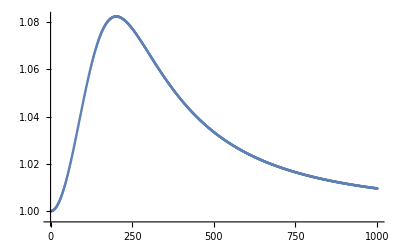

```mathematica
L=4;
g=2;
ks=Table[(2*n*Pi)/L,{n,1,(L/2-1)}];an = Table[-Total[Table[k=ks[[l]];If[g==J && k==-L/2,0,4*Sqrt[g^2+(J)^2-(2*J*g*Cos[k])]],{l,1,Length[ks]}]],{J,0,10,.01}];

op[n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2,2}:=KroneckerProduct[IdentityMatrix[2^(k-1),SparseArray],a,IdentityMatrix[2^(n-k),SparseArray]];
sz[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[3]];
sx[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[1]];
HH[n_Integer/;n≥3,g_,J_]:=-g*Sum[sz[n,k],{k,n}]-J*Sum[sx[n,k].sx[n,Mod[k+1,n,1]],{k,n}];
num =Table[kk=HH[L,g,J]//Eigenvalues//Min;kk,{J,0,10,.01}];
ListPlot[an/num, PlotRange->All]
```